## Increment Implementation

### CA Base Functions

```mathematica
(* randomly select a rule *)
getRule[k_, r_]:=
	RandomInteger[{0, k^k^(2*r+1) - 1}]
	
(* all blocks of cells in the rule *)
getBlocks[k_, r_]:=
	Tuples[Reverse[Range[0, k-1, 1]], 2*r+1] 
	
(* rule in base of # colors *)
ruleDigits[n_, k_, r_]:=ruleDigits[n, k, r]=
	IntegerDigits[n, k, k^(2*r+1)]
	
(* ratio of uncompressed to compressed size of CA, good measure for classification *)
compressionRatio[ca_]:=N[ByteCount[ca]/ByteCount[Compress[ca]], 4] 

(* measure of difference between rules by summing squares of differences between rule applications - currently unused *)
difference[rule_,newRule_]:=Total[Abs[countUses[rule]-countUses[newRule]]]
```

### Rule Incrementing Functions

```mathematica
(* change the color of one replacement from the rule *)
ruleShift[{n_, k_, r_}, block_, shift_]:=ruleShift[{n, k, r}, block, shift]=
	With[{ruleLen = k^(2*r+1)},
		{
		FromDigits[Mod[IntegerDigits[n, k, ruleLen] + SparseArray[block->shift, ruleLen], k], k],
		k, r
		}
	]
	
(* count uses of each block of the rule in a ca *)
countUses[{n_, k_, r_}, init_, size_]:=countUses[{n, k, r}]=
	Lookup[Counts[Flatten[Partition[CellularAutomaton[{n, k, r}, init, size-1], {1, 2*r+1}], 2]], getBlocks[k, r], 0]
	
(* order of blocks to be replaced *)
blockOrder[ruleSpec_, init_, size_, nBlocks_, distance_]:=
	Ordering[countUses[ruleSpec, init, size], nBlocks + distance][[distance + 1 ;; ]] 

(* shift one block of rule *)
blockShifts[{n_, k_, r_}, block_]:=
	ruleShift[{n, k, r}, block, #]& /@ Table[i, {i, k-1}] 

(* make a tree of associations for all specified rule replacements *)
ruleReplace[ruleSpec_, {}]:=ruleSpec
ruleReplace[ruleSpec_, reps_]:=
	Map[ruleSpec -> iterateRules[#, Rest[reps]]&, blockShifts[ruleSpec, First[reps]]] 


			
			
(* final function *)
iterateRule[ruleSpec_, init_, size_, nBlocks_, distance_]:=
	ruleReplace[ruleSpec, blockOrder[ruleSpec, init, size, nBlocks, distance]]
```

```mathematica
(* make map suitable for graphing *)
connections[ruleSpec_, init_, size_, nBlocks_, distance_]:=
	ruleReplace[ruleSpec, blockOrder[ruleSpec, init, size, nBlocks, distance]] //.
		Rule[a_, {b__Rule}] :> {Rule[a,#]& /@ Keys[{b}], b} //
			Flatten // DeleteDuplicates
				
(* visualization *)
showRuleConnections[ruleSpec_, init_, size_, nBlocks_, distance_] :=
	Graph[connections[ruleSpec, init, size, nBlocks, distance],
		VertexShapeFunction :> (Inset[ArrayPlot[CellularAutomaton[#2, init, size-1], ImageSize->{100,100}], #1, Center, .6]&),
			ImagePadding->25, PlotRange->All, ImageSize->800
	]
```

## Testing

```mathematica
k = 2;
r = 1;
```

```mathematica
n = getRule[k, r]
```

213

```mathematica
size=50;
```

```mathematica
blocks = getBlocks[k, r]
```

{{1,1,1},{1,1,0},{1,0,1},{1,0,0},{0,1,1},{0,1,0},{0,0,1},{0,0,0}}

```mathematica
digits = ruleDigits[n,k,r]
```

{1,1,0,1,0,1,0,1}

```mathematica
init = RandomInteger[1,50];
```

```mathematica
countUses[{n,k,r}, init, 50]
```

{63,178,18,173,175,15,173,5}

```mathematica
blockOrder[{n,k,r}, init, size, 3, 1]
```

{6,3,1}

```mathematica
blockShifts[{n,k,r}, 2]
```

{{149,2,1}}

```mathematica
ruleReplace[{n, k, r}, blockOrder[{n,k,r}, init, size, 3, 1]]
```

{{213,2,1}→{{209,2,1}→{{241,2,1}→{113,2,1}}}}

```mathematica
connections[{n, k, r}, init, size, 3, 1]
```

{{213,2,1}→{209,2,1},{209,2,1}→{241,2,1},{241,2,1}→{113,2,1}}

```mathematica
iterateRule[{n,k,r}, init, size, 3, 1]
```

{{213,2,1}→{{209,2,1}→{{241,2,1}→{113,2,1}}}}

```mathematica
iterateRule[{n,k,r}, init, size, 3, 2]
```

{{213,2,1}→{{245,2,1}→{{117,2,1}→{101,2,1}}}}

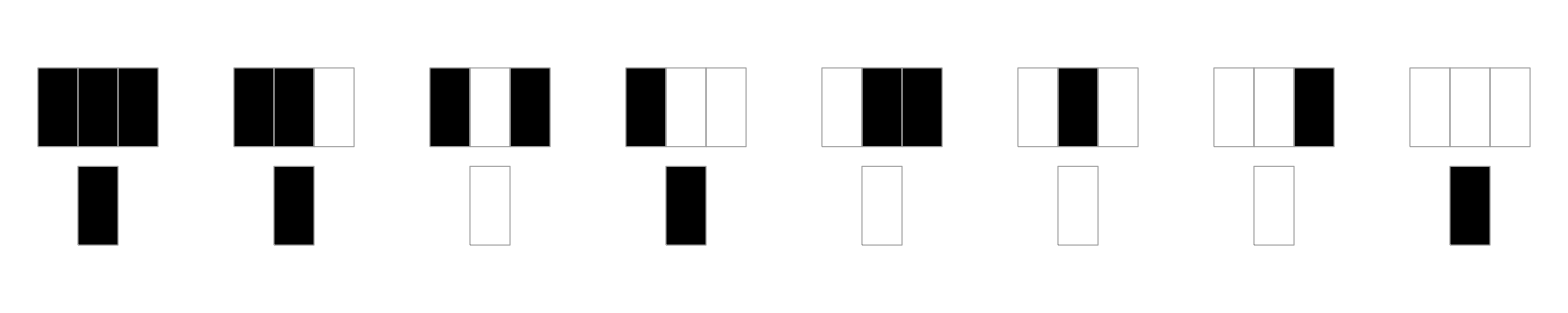

```mathematica
RulePlot[CellularAutomaton[{209,2,1}]]
```

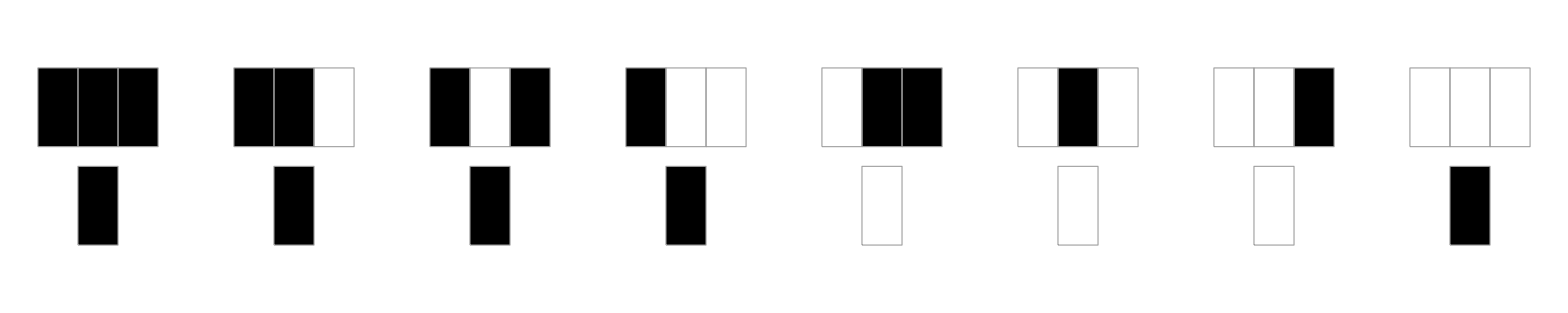

```mathematica
RulePlot[CellularAutomaton[{241,2,1}]]
```

```mathematica
showRuleConnections[{n,k,r}, init, size, 3, 0]
```

-Graphics-

```mathematica
connections[{n,k,r}, init, size, 3, 0]
```

{{213,2,1}→{212,2,1},{212,2,1}→{208,2,1},{208,2,1}→{240,2,1}}